# Mathematica NDSolve

```mathematica
s=NDSolve[{x'[t]==y[t],y'[t]==-0.25 y[t]+x[t]-(x[t])^3+0.25 Cos[t],y[0]==0,x[0]==0},{x,y},{t,0,100}]//FullSimplify
```

{{x→InterpolatingFunction[{{0., 100.}}, <>],y→InterpolatingFunction[{{0., 100.}}, <>]}}

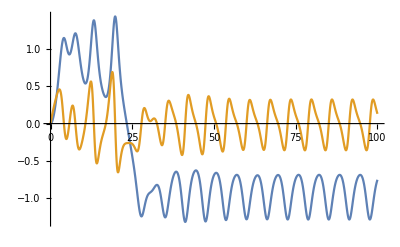

```mathematica
Plot[{x[t]/.s[[1]],y[t]/.s[[1]]},{t,0,100}]
```

# Explicit Euler Method

```mathematica
eem[δt_, tmaxim_,xint_,yint_,F_,ω_,μ_]:=Module[{fst,iter,poin,coords,poincoords,traj,proj,strobtraj,poinsec},
fst[Δt_,tmax_,u0_,v0_]:=NestList[{#1⟦1⟧+Δt #1⟦2⟧,#1⟦2⟧-μ Δt #1⟦2⟧+ Δt #1⟦1⟧- (Δt #1⟦1⟧)^3+F Cos[#1[[3]] ω],#1⟦3⟧+Δt}&,{u0,v0,0},Floor[tmax/Δt]];
iter=fst[δt  ,tmaxim,xint ,yint ];
poin=Table[iter[[i]],{i,1,Length[iter],1/δt}];
coords=Map[{{#1[[3]],#1[[1]]},{#1[[3]],#1[[2]]}}&,iter];
poincoords=Map[{{#1[[3]],#1[[1]]},{#1[[3]],#1[[2]]}}&,poin];
traj=ListPlot[Flatten[coords,{2}],Joined-> True,ImageSize-> {400,200}];
proj=ListPlot[Map[Drop[#1,-1]&,iter],ImageSize-> {300,220}];
strobtraj=ListPlot[Flatten[poincoords,{2}],Joined-> True,ImageSize-> {400,200}];
poinsec=ListPlot[Map[Drop[#1,-1]&,poin],ImageSize-> {300,220}];
Grid[{{traj},{strobtraj},{proj},{poinsec}}]]
```

```mathematica
eem[0.01,100000,0,0,2.7,1,0.22]
```

-Graphics-

# RK-4

```mathematica
rungekutta[δt_, tmaxim_,xint_,yint_,F_,ω_,μ_]:=Module[{funcx,funcy,force,omega,fnext,f,iter,poin,coords,poincoords,traj,proj,strobtraj,poinsec},
funcx[t_,x_ ,y_]:=y;
funcy[t_,x_,y_]:=-μ y+x-x^3+force Cos[omega t]/.force-> F/.omega-> ω;
fnext[x_,y_,t_,h_,f_]:=Module[{k1,k2,k3,k4},
k1=h f[t,x,y];
k2=h f[t +(0.5  h),x +0.5 k1,y+0.5 k1];
k3 =h f[t+(0.5 h),x+0.5 k2,y+0.5 k2];
k4=h f[t+h,x+k3,y+k3];
{ x+1/6 k1+1/3 k2+1/3 k3+1/6 k4,y+1/6 k1+1/3 k2+1/3 k3+1/6 k4}];
f[h_,max_,xinit_,yinit_,t_,fx_,fy_]:=NestList[{#⟦1⟧+h,fnext[#⟦2⟧,#⟦3⟧,#⟦1⟧,h,fx][[1]],fnext[#⟦2⟧,#⟦3⟧,#⟦1⟧,h,fy][[2]]}&,{t,xinit,yinit},Floor[max/h]];
iter=f[δt ,tmaxim,xint,yint,0,funcx,funcy];
poin=Table[iter[[i]],{i,1,Length[iter],Floor[(2π)/δt]}];
coords=Transpose[Map[{{#1[[1]],#1[[2]]},{#1[[1]],#1[[3]]}}&,iter]];
poincoords=Transpose[Map[{{#1[[1]],#1[[2]]},{#1[[1]],#1[[3]]}}&,poin]];
traj=ListPlot[coords,Joined-> True,ImageSize-> {400,200},AxesLabel-> {"t",Style["x",Bold]}];
proj=ListPlot[Map[Drop[#1,1]&,iter],ImageSize-> {300,220},AxesLabel-> {"x_1","x_2"}];
strobtraj=ListPlot[poincoords,Joined-> True,ImageSize-> {400,200},AxesLabel-> {"t",Style["x",Bold]}];
poinsec=ListPlot[Map[Drop[#1,1]&,poin],ImageSize-> {300,220},AxesLabel-> {"x_1","x_2"}];
Grid[{{traj},{strobtraj},{proj},{poinsec}}]]
```

```mathematica
Manipulate[rungekutta[0.01,100,0,0,1,ω,0.25],{ω,0,4}]
```